# Nbody0 test

## Data input

```mathematica
datatable=Import["/home/lswl/Documents/works/Datas/Astrophysics/Calculation/Nbody/test.log","Table"];
```

```mathematica
datatable=Import["D:/Documents/works/Datas/Astrophysics/Calculation/Nbody/moon.log","Table"];
```

## Table structure:

1. Bodys, times, Nsteps, Energy
2. Bodys: R, V, M，Step

```mathematica
Tottime=50;
timeinv=0.002;
numb=4;
Rstars={0.1,0.1,0.04,0.05};

timestep=Min[Tottime/timeinv,Length[datatable]/(numb+1)//N]
Radius=Table[Table[{datatable[[r,6]]-datatable[[r-i+1,6]],datatable[[r,7]]-datatable[[r-i+1,7]],datatable[[r,8]]-datatable[[r-i+1,8]]},{r,i,(timestep-1)*(numb+1)+i,numb+1}],{i,1,numb,1}];
velocity=Table[Table[{datatable[[r,9]],datatable[[r,10]],datatable[[r,11]]},{r,i,(timestep-1)*(numb+1)+i,numb+1}],{i,1,numb,1}];

mass=Table[datatable[[i,5]],{i,1,numb,1}];
steps=Table[Table[datatable[[r,12]],{r,i,(timestep-1)*(numb+1)+i,numb+1}],{i,1,numb,1}];
timelist=Table[datatable[[i,3]],{i,numb+1,timestep*(numb+1),numb+1}];
Nsteps=Table[datatable[[i,6]],{i,numb+1,timestep*(numb+1),numb+1}];
Energylist=Table[datatable[[i,9]],{i,numb+1,timestep*(numb+1),numb+1}];
```

25000.

```mathematica
Rfun=Table[Interpolation[Table[{timelist[[i]],Radius[[j,i]]},{i,1,timestep,1}]],{j,1,numb,1}]
```

{InterpolatingFunction[{{0.,49.998}},<>],InterpolatingFunction[{{0.,49.998}},<>],InterpolatingFunction[{{0.,49.998}},<>],InterpolatingFunction[{{0.,49.998}},<>]}

```mathematica
relv=velocity[[3]]-velocity[[2]];
```

```mathematica
ListAnimate[Table[Graphics3D[Table[{RGBColor[j/numb,1-j/numb,j/numb],Sphere[Radius[[j,i]],Rstars[[j]]]},{j,1,numb,1}],AxesLabel->{"x","y","z"},PlotRange-> {{-1.2,1.2},{-1.2,1.2},{-1,1}},ViewPoint->{1,1,1}],{i,1,timestep,10}]]
```

```mathematica
Animate[Graphics3D[Table[{RGBColor[j/numb,1-j/numb,j/numb],Sphere[Rfun[[j]][a],Rstars[[j]]]},{j,1,numb,1}],AxesLabel->{"x","y","z"},PlotRange-> {{-10,10},{-10,10},{-10,10}},ViewPoint->{0,0,1}],{a,0,Tottime}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

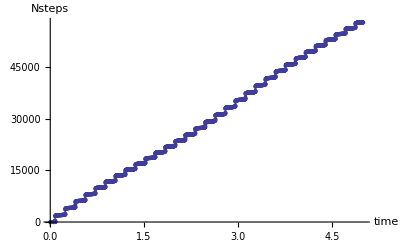

Mesh::ilevels: 2500. is not a valid mesh specification.

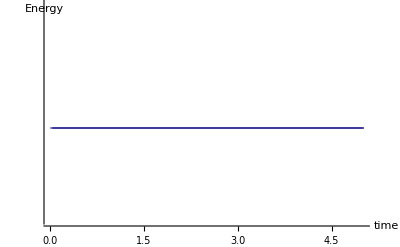

```mathematica
ListPointPlot3D[Radius,AxesLabel->{"x","y","z"},PlotStyle->{Red,Blue,Black}]
ListPointPlot3D[velocity,AxesLabel->{"v_x","v_y","v_z"},PlotStyle->{Red,Blue,Black}]
ListPointPlot3D[relv,AxesLabel->{"v_x","v_y","v_z"},PlotStyle->Black]
ListPlot[Transpose[{timelist,Nsteps}],Joined->True,Mesh->All,AxesLabel->{"time","Nsteps"}]
ListPlot[Transpose[{timelist,Energylist}],Joined->True,Mesh->timestep,InterpolationOrder->2,AxesLabel->{"time","Energy"}]
```

Solar-Earth-Moon system

### Observation data

#### Sun

Distance 1.496*^8 km
Mass 1.9891*^30

```mathematica
Sunmass=1;
```

#### Earth

Mass 5.9736*^24  0.0334349 Sun

```mathematica
Earthmass=5.9736*^24/1.9891*^30
EarthD=1;
```

3.00317×10^-6

#### Moon

Distance 0.0024-0.0027AU
Mass 0.0123Earth

```mathematica
Moonmass=0.0123*Earthmass
MoonD=1.0025;
```

3.6939×10^-8

### Calculation

#### Moon

```mathematica
moonR=MoonD-EarthD
vmoon=√(Sunmass/MoonD^2+Earthmass/(MoonD-EarthD)^2)*moonR
```

0.0025

0.00303678

#### Sun:

```mathematica
sunR=(Earthmass*EarthD+Moonmass*MoonD)/(Earthmass+Moonmass+Sunmass)
vsun=√(Earthmass/EarthD^2+Moonmass/MoonD^2)*sunR
```

0.000415109

8.42787×10^-6

#### Earth:

```mathematica
earthR=EarthD-sunR
vearth=√(Sunmass/EarthD^2-Moonmass/MoonD^2)*earthR
```

0.999585

0.99938